31

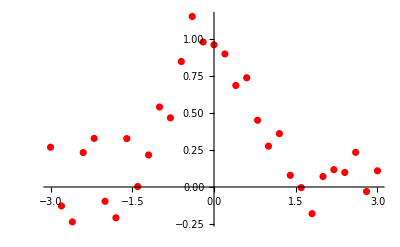

```mathematica
data=Table[x->Exp[-x^2]+RandomVariate[NormalDistribution[0,.15]],{x,-3,3,.2}];
Length[data]
plot=ListPlot[List@@@data,PlotStyle->Red]
```

```mathematica
{testD,trainD} = TakeDrop[RandomSample@data,5];
```

```mathematica
net2 = NetChain[{LinearLayer[100],ElementwiseLayer[Tanh],LinearLayer[1]},"Input"->"Scalar","Output"->"Scalar"];

net2 = NetChain[{LinearLayer[100],DropoutLayer[0.3],ElementwiseLayer[Tanh],LinearLayer[100],ElementwiseLayer[Tanh],LinearLayer[]},"Input"->"Scalar","Output"->"Scalar"];
net2T = NetTrain[net2,data,All,ValidationSet->Scaled[0.1]]
```

NetTrainResultsObject[<>]

```mathematica
net2T = NetTrain[net2,trainD,All,ValidationSet->trainD]
```

NetTrainResultsObject[<>]

```mathematica
(*Most common regression loss funciton*)
```

```mathematica
loss = MeanSquaredLossLayer[]
```

MeanSquaredLossLayer[<>]

```mathematica
loss@<|"Input"->3,"Target"->4|>
```

1.

```mathematica
(*Another common loss*)
```

```mathematica
loss2 = MeanAbsoluteLossLayer[]
```

MeanAbsoluteLossLayer[<>]

```mathematica
predict = <|"cat"->0.2,"dog"->0.8|>;
target = "cat";

CrossEntropyLossLayer["Index"]@<|"Input"->{0.05,0.95},"Target"->1|>
```

2.99573

```mathematica
plot=ListPlot[List@@@data,PlotStyle->Red]
```

-Graphics-

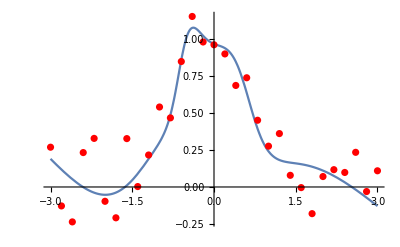

```mathematica
Show[Plot[net2T[x],{x,-3,3}],plot,PlotRange->All]
```

```mathematica
net2 = NetChain[{LinearLayer[100],ElementwiseLayer[Tanh],LinearLayer[]}]
```

NetChain[<>]

```mathematica
floss [x_,y_] := (x-y)^4;
```

```mathematica
loss = NetGraph[<|"thread"->ThreadingLayer[(#1-#2)^4&]|>,{NetPort["Input"]->"thread",NetPort["Target"]->"thread"}]
```

NetGraph[<>]

```mathematica
net2T = NetTrain[net2,trainD,LossFunction->loss,ValidationSet->trainD]
```

NetChain[<>]

```mathematica
net2=NetChain[{LinearLayer[10],ElementwiseLayer[Tanh],LinearLayer[]}]
trainNet = NetGraph[<|"net"->net2,"loss1"->MeanSquaredLossLayer[],"loss2"->MeanAbsoluteLossLayer[],"plus"->ThreadingLayer[Plus]|>,{"net"->NetPort["loss1","Input"],"net"->NetPort["loss2","Input"],{"loss1","loss2"}->"plus"}]
```

NetChain[<>]

NetGraph[<>]

```mathematica
dataAssoc = <|"Input"->data[[;;,1]],"Target"->data[[;;,2]]|>
```

<|Input→{-3.,-2.8,-2.6,-2.4,-2.2,-2.,-1.8,-1.6,-1.4,-1.2,-1.,-0.8,-0.6,-0.4,-0.2,0.,0.2,0.4,0.6,0.8,1.,1.2,1.4,1.6,1.8,2.,2.2,2.4,2.6,2.8,3.},Target→{0.269032,-0.128194,-0.236132,0.232713,0.328588,-0.0968683,-0.208451,0.32716,0.00285752,0.21629,0.540805,0.467421,0.848455,1.15318,0.980558,0.961544,0.8998,0.686596,0.738614,0.451308,0.276078,0.361117,0.0788934,-0.00429343,-0.180372,0.0706032,0.117036,0.098165,0.234383,-0.0308038,0.109514}|>

```mathematica
net3T = NetTrain[trainNet,dataAssoc,LossFunction->"Output"]
```

NetGraph[<>]

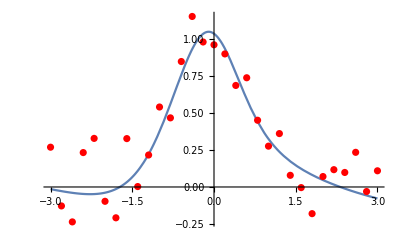

```mathematica
Show[Plot[net2T[x],{x,-3,3}],plot,PlotRange->All]
```

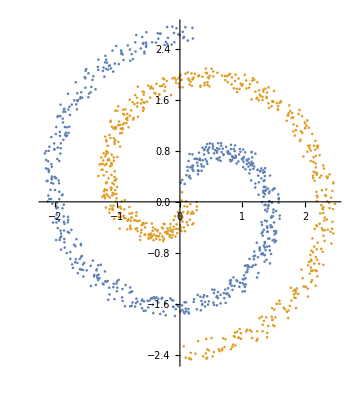

```mathematica
data1=N@Table[t^.5{Sin[t],Cos[t]}+RandomReal[.3,2],{t,.01,2Pi,.01}];
data2=N@Table[t^.5{Sin[t+Pi],Cos[t+Pi]}+RandomReal[.3,2],{t,.01,2Pi,.01}];
data=Thread[data1->1]~Join~Thread[data2->2];
ListPlot[{data1,data2},AspectRatio->Automatic]
```

```mathematica
c = Classify[data,Method->"NearestNeighbors"]
```

ClassifierFunction[…]

```mathematica
tableData = Table[c[{x,y}],{x,-3,3,0.1},{y,-3,3,0.1}];
```

```mathematica
ArrayPlot@tableData
```

-Graphics-

See the data

```mathematica
data[[1]]
```

{0.169158,0.366981}→1

SoftmaxLayer[] probability of the outputs, should use all the time!

```mathematica
net3 = NetInitialize@NetChain[{LinearLayer[10],ElementwiseLayer[Ramp],LinearLayer[2],SoftmaxLayer[]}, "Output"->NetDecoder[{"Class",{1,2}}],"Input"->2]
```

NetChain[<>]

```mathematica
net3[{0.2,0.3},"Probabilities"]
```

<|1→0.553434,2→0.446566|>

```mathematica
net3T = NetTrain[net3, data,ValidationSet->data]
```

NetChain[<>]

```mathematica
tableData = Table[net3T[{x,y}],{x,-3,3,0.1},{y,-3,3,0.1}];
ArrayPlot@tableData
```

-Graphics-

```mathematica
net3 = NetInitialize@NetChain[{LinearLayer[10],ElementwiseLayer[Ramp],LinearLayer[2],SoftmaxLayer[]}, "Output"->NetDecoder[{"Class",{1,2}}],"Input"->2]
```

NetChain[<>]